### Rosenbrock

```mathematica
ClearAll[f,a,b,g,c,r,J,L,H,Hc]
f[x1_,x2_]:=(a-x1)^2+b(x2-x1^2)^2;
g[x1_,x2_]:=Grad[f[x1,x2],{x1,x2}];
c[x1_,x2_]:=r^2-x1^2-x2^2;
J[x1_,x2_]:={Grad[c[x1,x2],{x1,x2}]};
L[x1_,x2_,y_]:=f[x1,x2]-c[x1,x2]y;
H[x1_,x2_,y_]:=Grad[Grad[L[x1,x2,y],{x1,x2}],{x1,x2}];
Hc[x1_,x2_] := Grad[Grad[c[x1,x2],{x1,x2}],{x1,x2}];
Hf[x1_,x2_]:=Grad[g[x1,x2],{x1,x2}];
```

```mathematica
a = 1;
b = 100;
r = √2;
ClearAll[a,b,r]
MatrixForm@g[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@J[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@H[x1,x2,y]/.{x1->x1,x2->x2,y->y}
MatrixForm@Hc[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@Hf[x1,x2]/.{x1->x1,x2->x2}
```

(-2 (a-x1)-4 b x1 (-x1^2+x2)
2 b (-x1^2+x2))

(-2 x1 | -2 x2)

(2+8 b x1^2-4 b (-x1^2+x2)+2 y | -4 b x1
-4 b x1 | 2 b+2 y)

(-2 | 0
0 | -2)

(2+8 b x1^2-4 b (-x1^2+x2) | -4 b x1
-4 b x1 | 2 b)

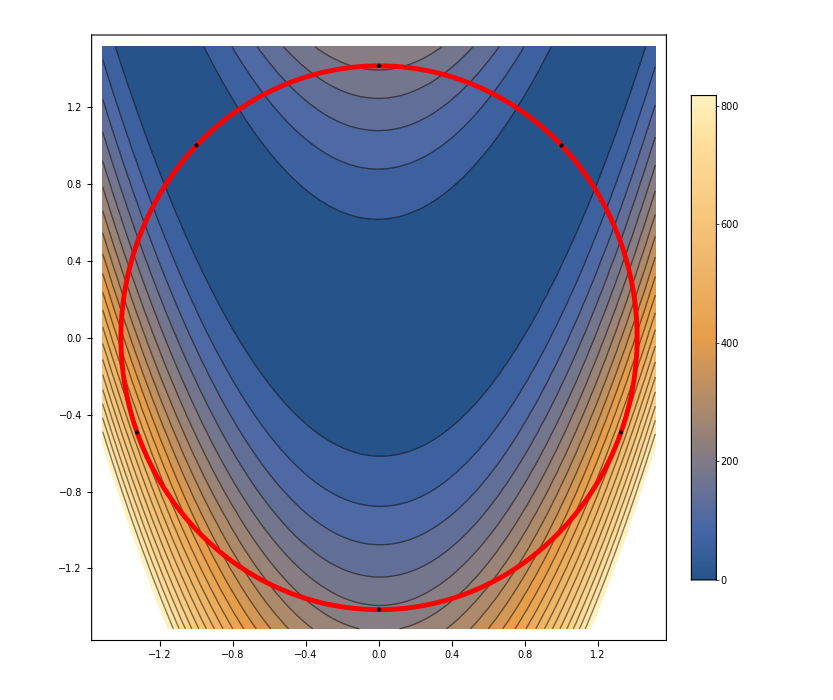

```mathematica
r = √2;
b=100;
a = 1;
pl1 = ContourPlot[f[x1,x2],{x1,-r-0.1,r+0.1},{x2,-r-0.1,r+0.1}, ImageSize->500,PlotLegends->Automatic,Contours->20];
pl2 = ParametricPlot[{r Cos[α],r Sin[α]},{α,0,2π},PlotStyle->{Red,Thickness[0.005]}];
pl3 = Graphics[{PointSize[Large],Point[{1,1}]}];
pl4 = Graphics[{PointSize[Large],Point[{-1,1}]}];
pl5 = Graphics[{PointSize[Large],Point[{-1.326,-0.492}]}];
pl6 = Graphics[{PointSize[Large],Point[{0,√2}]}];
pl7 = Graphics[{PointSize[Large],Point[{0,-√2}]}];
pl8 = Graphics[{PointSize[Large],Point[{1.326,-0.492}]}];
Show[pl1,pl2,pl3,pl4,pl5,pl6,pl7,pl8,ImageSize->700]
```

### Example 1

```mathematica
ClearAll[f,g,c,r,J,L,H]
f[x1_,x2_]:=x1 x2 - 1/2 x1^2-x2;
g[x1_,x2_]:=Grad[f[x1,x2],{x1,x2}];
c[x1_,x2_]:=r^2-x1^2-x2^2;
J[x1_,x2_]:={Grad[c[x1,x2],{x1,x2}]};
L[x1_,x2_,y_]:=f[x1,x2]-c[x1,x2]y;
H[x1_,x2_,y_]:=Grad[Grad[L[x1,x2,y],{x1,x2}],{x1,x2}];
Hc[x1_,x2_] := Grad[Grad[c[x1,x2],{x1,x2}],{x1,x2}];
Hf[x1_,x2_]:=Grad[g[x1,x2],{x1,x2}];
```

```mathematica
r = √2;
MatrixForm@g[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@J[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@H[x1,x2,y]/.{x1->x1,x2->x2,y->y}
MatrixForm@Hc[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@Hf[x1,x2]/.{x1->x1,x2->x2}
```

(-x1+x2
-1+x1)

(-2 x1 | -2 x2)

(-1+2 y | 1
1 | 2 y)

(-2 | 0
0 | -2)

(-1 | 1
1 | 0)

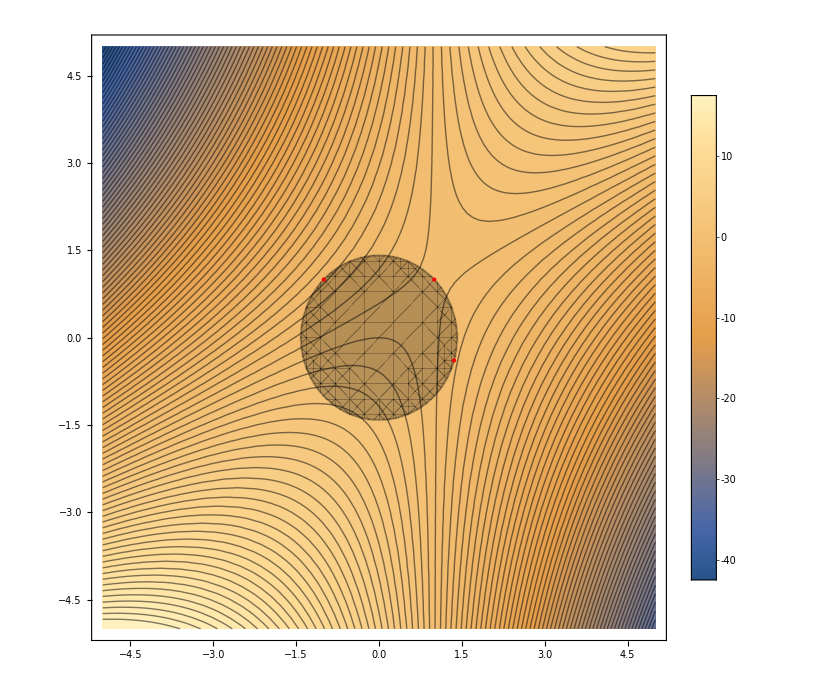

```mathematica
pl1 = ContourPlot[f[x1,x2],{x1,-5,5},{x2,-5,5}, ImageSize->500,PlotLegends->Automatic,Contours->100];
pl2 = RegionPlot[c[x1,x2]≥0,{x1,-5,5},{x2,-5,5},BoundaryStyle->Directive[Black,Opacity[0.25]],PlotStyle->Directive[Black,Opacity[0.25]]];
pmin1 = Graphics[{PointSize[Large],Red,Point[{-1,1}]}];
pmin2 = Graphics[{PointSize[Large],Red,Point[{1,1}]}];
pmin3 = Graphics[{PointSize[Large],Red,Point[{1.359,-0.39}]}];
Show[pl1,pl2,pmin1,pmin2,pmin3,ImageSize->700,Method->{"TransparentPolygonMesh"->True}]
```

### Example 2

```mathematica
ClearAll[f,g,c,J,L,H,Hc,Hf]
f[x1_,x2_]:=ⅇ^x1+x1^2+2 x1 x2+4 x2^2;
g[x1_,x2_]:=Grad[f[x1,x2],{x1,x2}];
c[x1_,x2_]:=x1+2 x2 -6;
J[x1_,x2_]:={Grad[c[x1,x2],{x1,x2}]};
L[x1_,x2_,y_]:=f[x1,x2]-c[x1,x2]y;
H[x1_,x2_,y_]:=Grad[Grad[L[x1,x2,y],{x1,x2}],{x1,x2}];
Hc[x1_,x2_] := Grad[Grad[c[x1,x2],{x1,x2}],{x1,x2}];
Hf[x1_,x2_]:=Grad[g[x1,x2],{x1,x2}];
```

```mathematica
MatrixForm@g[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@J[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@H[x1,x2,y]/.{x1->x1,x2->x2,y->y}
MatrixForm@Hc[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@Hf[x1,x2]/.{x1->x1,x2->x2}
```

(ⅇ^x1+2 x1+2 x2
2 x1+8 x2)

(1 | 2)

(2+ⅇ^x1 | 2
2 | 8)

(0 | 0
0 | 0)

(2+ⅇ^x1 | 2
2 | 8)

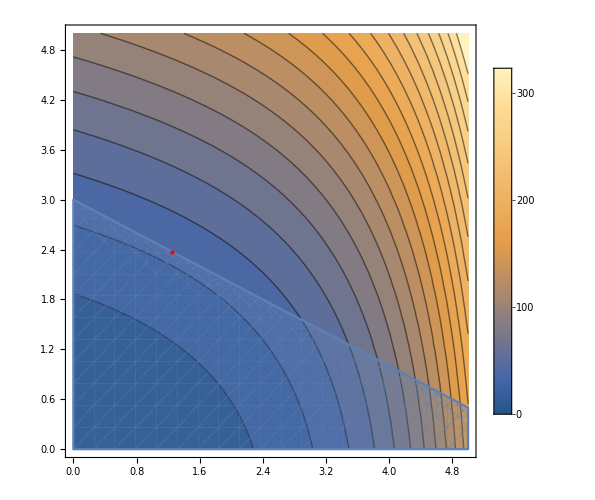

```mathematica
pl1 = ContourPlot[f[x1,x2],{x1,0,5},{x2,0,5}, ImageSize->500,PlotLegends->Automatic,Contours->20];
pl2 = RegionPlot[-c[x1,x2]≥0,{x1,0,5},{x2,0,5}, ImageSize->500];
pmin1 = Graphics[{PointSize[Large],Red,Point[{1.252,2.374}]}];
Show[pl1,pl2,pmin1]
```

### Example 3

```mathematica
ClearAll[f,g,c,J,L,H,Hc,Hf]
f[x1_,x2_,x3_,x4_,x5_]:=(x1-1)^2+(x1-x2)^2+(x2-x3)^2+(x3-x4)^2+(x4-x5)^2;
g[x1_,x2_,x3_,x4_,x5_]:=Grad[f[x1,x2,x3,x4,x5],{x1,x2,x3,x4,x5}];
c[x1_,x2_,x3_,x4_,x5_]:=({{x1+x2^2+x3^3-2-3 √2}, {x2-x3^2+x4+2-2 √2}, {x1 x5-2}});
J[x1_,x2_,x3_,x4_,x5_]:={Grad[c[x1,x2,x3,x4,x5],{x1,x2,x3,x4,x5}]}ᵀ;
L[x1_,x2_,x3_,x4_,x5_,y_]:=f[x1,x2,x3,x4,x5]-c[x1,x2,x3,x4,x5]y;
H[x1_,x2_,x3_,x4_,x5_,y_]:=Grad[Grad[L[x1,x2,x3,x4,x5,y],{x1,x2,x3,x4,x5}],{x1,x2,x3,x4,x5}];
Hc[x1_,x2_,x3_,x4_,x5_] := Grad[Grad[c[x1,x2,x3,x4,x5],{x1,x2,x3,x4,x5}],{x1,x2,x3,x4,x5}];
Hf[x1_,x2_,x3_,x4_,x5_]:=Grad[g[x1,x2,x3,x4,x5],{x1,x2,x3,x4,x5}];
```

```mathematica
MatrixForm@Simplify[g[x1,x2,x3,x4,x5]/.{x1->x1,x2->x2,x3->x3,x4->x4,x5->x5}]
MatrixForm@Simplify[J[x1,x2,x3,x4,x5]/.{x1->x1,x2->x2,x3->x3,x4->x4,x5->x5}]
MatrixForm@Simplify[H[x1,x2,x3,x4,x5,y]/.{x1->x1,x2->x2,x3->x3,x4->x4,x5->x5,y->y}]
MatrixForm@Simplify[Hc[x1,x2,x3,x4,x5]/.{x1->x1,x2->x2,x3->x3,x4->x4,x5->x5}]
MatrixForm@Simplify[Hf[x1,x2,x3,x4,x5]/.{x1->x1,x2->x2,x3->x3,x4->x4,x5->x5}]
```

(4 x1-2 (1+x2)
-2 (x1-2 x2+x3)
-2 (x2-2 x3+x4)
-2 (x3-2 x4+x5)
-2 x4+2 x5)

((1 | 2 x2 | 3 x3^2 | 0 | 0)
(0 | 1 | -2 x3 | 1 | 0)
(x5 | 0 | 0 | 0 | x1))

((4 | -2 | 0 | 0 | 0
-2 | 4-2 y | -2 | 0 | 0
0 | -2 | 4-6 x3 y | -2 | 0
0 | 0 | -2 | 4 | -2
0 | 0 | 0 | -2 | 2)
(4 | -2 | 0 | 0 | 0
-2 | 4 | -2 | 0 | 0
0 | -2 | 2 (2+y) | -2 | 0
0 | 0 | -2 | 4 | -2
0 | 0 | 0 | -2 | 2)
(4 | -2 | 0 | 0 | -y
-2 | 4 | -2 | 0 | 0
0 | -2 | 4 | -2 | 0
0 | 0 | -2 | 4 | -2
-y | 0 | 0 | -2 | 2))

((0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 6 x3 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0))

(4 | -2 | 0 | 0 | 0
-2 | 4 | -2 | 0 | 0
0 | -2 | 4 | -2 | 0
0 | 0 | -2 | 4 | -2
0 | 0 | 0 | -2 | 2)

### Maratos

```mathematica
ClearAll[f,a,b,g,c,r,J,L,H,Hc]
f[x1_,x2_]:=-x1+2(x1^2+x2^2-1);
g[x1_,x2_]:=Grad[f[x1,x2],{x1,x2}];
c[x1_,x2_]:=1-(x1^2+x2^2);
J[x1_,x2_]:={Grad[c[x1,x2],{x1,x2}]};
L[x1_,x2_,y_]:=f[x1,x2]-c[x1,x2]y;
H[x1_,x2_,y_]:=Grad[Grad[L[x1,x2,y],{x1,x2}],{x1,x2}];
Hc[x1_,x2_] := Grad[Grad[c[x1,x2],{x1,x2}],{x1,x2}];
Hf[x1_,x2_]:=Grad[g[x1,x2],{x1,x2}];
```

```mathematica
MatrixForm@g[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@J[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@H[x1,x2,y]/.{x1->x1,x2->x2,y->y}
MatrixForm@Hc[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@Hf[x1,x2]/.{x1->x1,x2->x2}
```

(-1+4 x1
4 x2)

(-2 x1 | -2 x2)

(4+2 y | 0
0 | 4+2 y)

(-2 | 0
0 | -2)

(4 | 0
0 | 4)

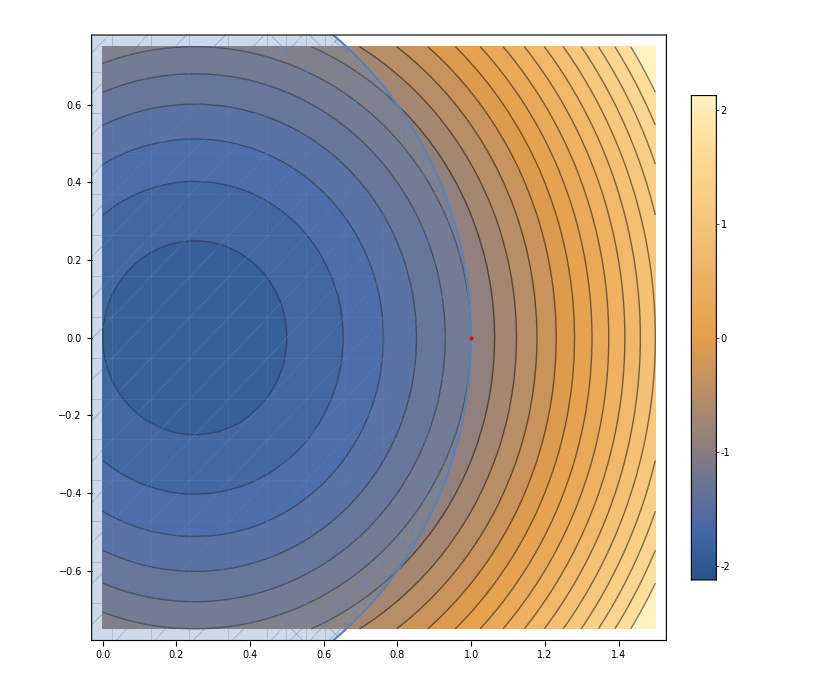

```mathematica
pl1 = ContourPlot[f[x1,x2],{x1,-0,1.5},{x2,-0.75,0.75}, ImageSize->500,PlotLegends->Automatic,Contours->20];
pl2 = RegionPlot[c[x1,x2]≥0,{x1,-0.5,1.5},{x2,-1,1}];
pmin = Graphics[{PointSize[Large],Red,Point[{1,0}]}];
Show[pl1,pl2,pmin,ImageSize->700]
```

### Example 5

```mathematica
ClearAll[f,g,c,r,J,L,H]
f[x1_,x2_]:=x1 x2 - 1/2 x1^2-x2;
g[x1_,x2_]:=Grad[f[x1,x2],{x1,x2}];
c[x1_,x2_]:=({{-3x1+x2+3}, {2x1+x2+3}, {-x2+2}});
J[x1_,x2_]:={Grad[c[x1,x2],{x1,x2}]};
L[x1_,x2_,y_]:=f[x1,x2]-c[x1,x2]y;
H[x1_,x2_,y_]:=Grad[Grad[L[x1,x2,y],{x1,x2}],{x1,x2}];
Hc[x1_,x2_] := Grad[Grad[c[x1,x2],{x1,x2}],{x1,x2}];
Hf[x1_,x2_]:=Grad[g[x1,x2],{x1,x2}];
```

```mathematica
r = √2;
ClearAll[a,b,r]
MatrixForm@g[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@J[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@H[x1,x2,y]/.{x1->x1,x2->x2,y->y}
MatrixForm@Hc[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@Hf[x1,x2]/.{x1->x1,x2->x2}
```

(-x1+x2
-1+x1)

((-3 | 1) | (2 | 1) | (0 | -1))

((-1 | 1
1 | 0)
(-1 | 1
1 | 0)
(-1 | 1
1 | 0))

((0 | 0
0 | 0)
(0 | 0
0 | 0)
(0 | 0
0 | 0))

(-1 | 1
1 | 0)

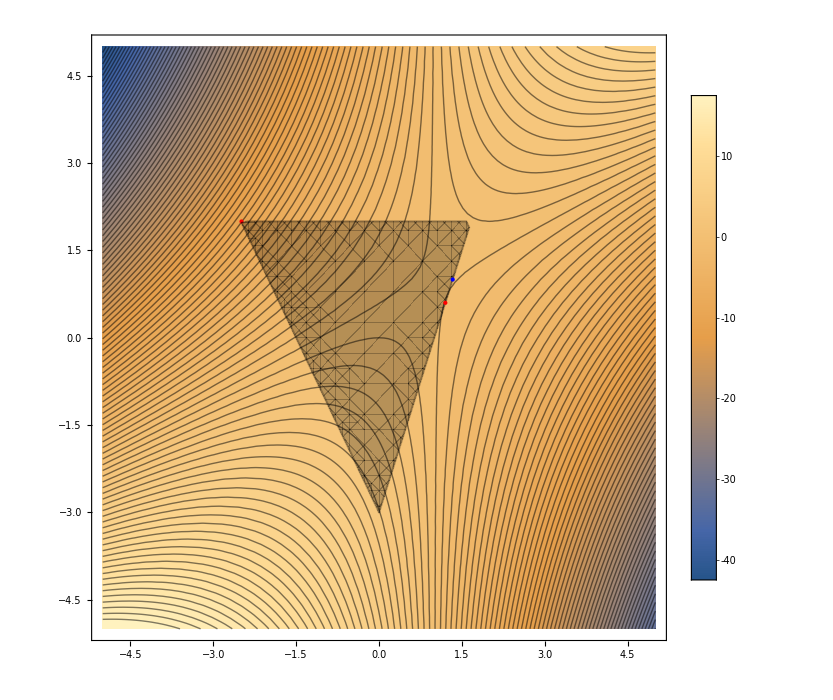

-10.125

(25/2
0
0)

-0.6

(0
6
7/5)

```mathematica
pl1 = ContourPlot[f[x1,x2],{x1,-5,5},{x2,-5,5}, ImageSize->500,PlotLegends->Automatic,Contours->100];
pl2 = RegionPlot[{-3x1+3+x2≥0&&2x1+3+x2≥0&&-x2+2≥0},{x1,-5,5},{x2,-5,5},BoundaryStyle->Directive[Black,Opacity[0.25]],PlotStyle->Directive[Black,Opacity[0.25]]];
pmin1 = Graphics[{PointSize[Large],Red,Point[{-5/2,2}]}];
pmin2 = Graphics[{PointSize[Large],Red,Point[{6/5,3/5}]}];
ptest = Graphics[{PointSize[Large],Blue,Point[{4/3,1}]}];
Show[pl1,pl2,pmin1,pmin2,ptest,ImageSize->700,Method->{"TransparentPolygonMesh"->True}]
f[-5./2,2]
MatrixForm@c[-5/2,2]
f[6./5,3/5]
MatrixForm@c[6/5,3/5]
```

### Example 6

```mathematica
ClearAll[f,g,c,r,J,L,H,x1,x2]
f[x1_,x2_]:=3x1 - x2+x1^2+3/2 x2^2;
g[x1_,x2_]:=Grad[f[x1,x2],{x1,x2}];
c[x1_,x2_]:=({{-3(x1-2)^2+x2+3}, {2(x1-2)^2+x2+3}});
J[x1_,x2_]:={Expand[Grad[c[x1,x2],{x1,x2}]]};
L[x1_,x2_,y_]:=f[x1,x2]-c[x1,x2]y;
H[x1_,x2_,y_]:=Grad[Grad[L[x1,x2,y],{x1,x2}],{x1,x2}];
Hc[x1_,x2_] := Grad[Grad[c[x1,x2],{x1,x2}],{x1,x2}];
Hf[x1_,x2_]:=Grad[g[x1,x2],{x1,x2}];
```

```mathematica
ClearAll[a,b]
MatrixForm@g[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@J[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@H[x1,x2,y]/.{x1->x1,x2->x2,y->y}
MatrixForm@Hc[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@Hf[x1,x2]/.{x1->x1,x2->x2}
```

(3+2 x1
-1+3 x2)

((12-6 x1 | 1) | (-8+4 x1 | 1))

((2+6 y | 0
0 | 3)
(2-4 y | 0
0 | 3))

((-6 | 0
0 | 0)
(4 | 0
0 | 0))

(2 | 0
0 | 3)

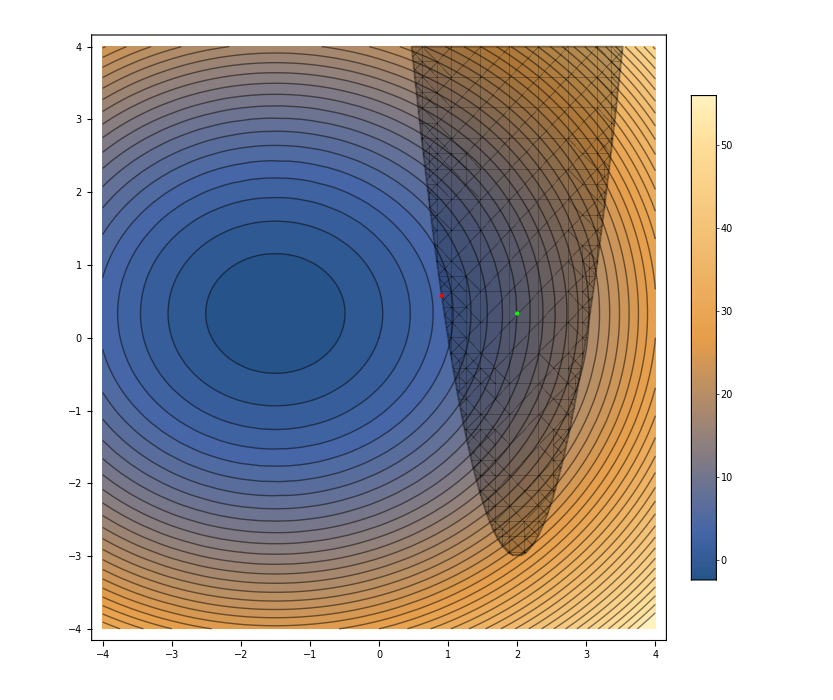

-1.47748

```mathematica
pl1 = ContourPlot[f[x1,x2],{x1,-4,4},{x2,-4,4}, ImageSize->500,PlotLegends->Automatic,Contours->40];
pl2 = RegionPlot[{-3(x1-2)^2+x2+3≥0&&2(x1-2)^2+x2+3≥0},{x1,-4,4},{x2,-4,4},BoundaryStyle->Directive[Black,Opacity[0.25]],PlotStyle->Directive[Black,Opacity[0.25]]];
pmin1 = Graphics[{PointSize[Large],Red,Point[{0.9079,0.5783}]}];
ptest = Graphics[{PointSize[Large],Green,Point[{2,1/3}]}];
Show[pl1,pl2,pmin1,ptest,ImageSize->700,Method->{"TransparentPolygonMesh"->True}]
f[-0.7103,0.792]
```

### Example 7

```mathematica
ClearAll[f,g,c,r,J,L,H,x1,x2]
f[x1_,x2_]:=3x1 - x2+x1^2+3/2 x2^2;
g[x1_,x2_]:=Grad[f[x1,x2],{x1,x2}];
c[x1_,x2_]:=({{-3(x1+2)^2+x2+3}, {2(x1+2)^2+x2+3}});
J[x1_,x2_]:={Expand[Grad[c[x1,x2],{x1,x2}]]};
L[x1_,x2_,y_]:=f[x1,x2]-c[x1,x2]y;
H[x1_,x2_,y_]:=Grad[Grad[L[x1,x2,y],{x1,x2}],{x1,x2}];
Hc[x1_,x2_] := Grad[Grad[c[x1,x2],{x1,x2}],{x1,x2}];
Hf[x1_,x2_]:=Grad[g[x1,x2],{x1,x2}];
```

```mathematica
ClearAll[a,b]
MatrixForm@g[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@J[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@H[x1,x2,y]/.{x1->x1,x2->x2,y->y}
MatrixForm@Hc[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@Hf[x1,x2]/.{x1->x1,x2->x2}
```

(3+2 x1
-1+3 x2)

((-12-6 x1 | 1) | (8+4 x1 | 1))

((2+6 y | 0
0 | 3)
(2-4 y | 0
0 | 3))

((-6 | 0
0 | 0)
(4 | 0
0 | 0))

(2 | 0
0 | 3)

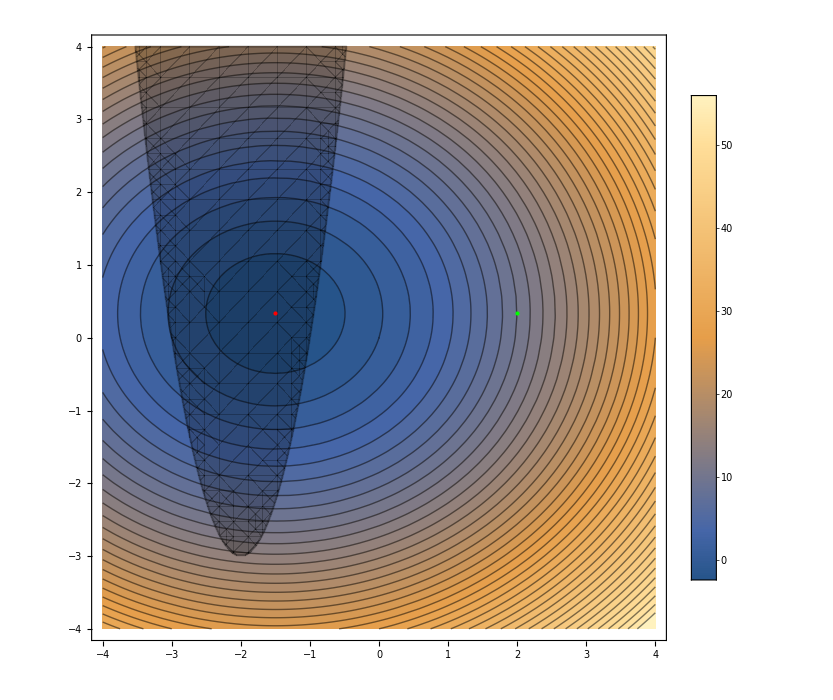

-1.47748

```mathematica
pl1 = ContourPlot[f[x1,x2],{x1,-4,4},{x2,-4,4}, ImageSize->500,PlotLegends->Automatic,Contours->40];
pl2 = RegionPlot[{-3(x1+2)^2+x2+3≥0&&2(x1+2)^2+x2+3≥0},{x1,-4,4},{x2,-4,4},BoundaryStyle->Directive[Black,Opacity[0.25]],PlotStyle->Directive[Black,Opacity[0.25]]];
pmin1 = Graphics[{PointSize[Large],Red,Point[{-1.5,1/3}]}];
ptest = Graphics[{PointSize[Large],Green,Point[{2,1/3}]}];
Show[pl1,pl2,pmin1,ptest,ImageSize->700,Method->{"TransparentPolygonMesh"->True}]
f[-0.7103,0.792]
```

### Example 8

```mathematica
ClearAll[f,g,c,r,J,L,H,x1,x2]
f[x1_,x2_]:=1/4 x1^2+x2^2+3 x1 x2-3x1-6x2;
g[x1_,x2_]:=Grad[f[x1,x2],{x1,x2}];
c[x1_,x2_]:=({{-5/2 x1+x2+19/4}, {x1-1/2}, {x2-1/2}});
J[x1_,x2_]:={Expand[Grad[c[x1,x2],{x1,x2}]]};
L[x1_,x2_,y_]:=f[x1,x2]-c[x1,x2]y;
H[x1_,x2_,y_]:=Grad[Grad[L[x1,x2,y],{x1,x2}],{x1,x2}];
Hc[x1_,x2_] := Grad[Grad[c[x1,x2],{x1,x2}],{x1,x2}];
Hf[x1_,x2_]:=Grad[g[x1,x2],{x1,x2}];
```

```mathematica
ClearAll[a,b]
MatrixForm@g[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@J[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@H[x1,x2,y]/.{x1->x1,x2->x2,y->y}
MatrixForm@Hc[x1,x2]/.{x1->x1,x2->x2}
MatrixForm@Hf[x1,x2]/.{x1->x1,x2->x2}
```

(-3+x1/2+3 x2
-6+3 x1+2 x2)

((-5/2 | 1) | (1 | 0) | (0 | 1))

((1/2 | 3
3 | 2)
(1/2 | 3
3 | 2)
(1/2 | 3
3 | 2))

((0 | 0
0 | 0)
(0 | 0
0 | 0)
(0 | 0
0 | 0))

(1/2 | 3
3 | 2)

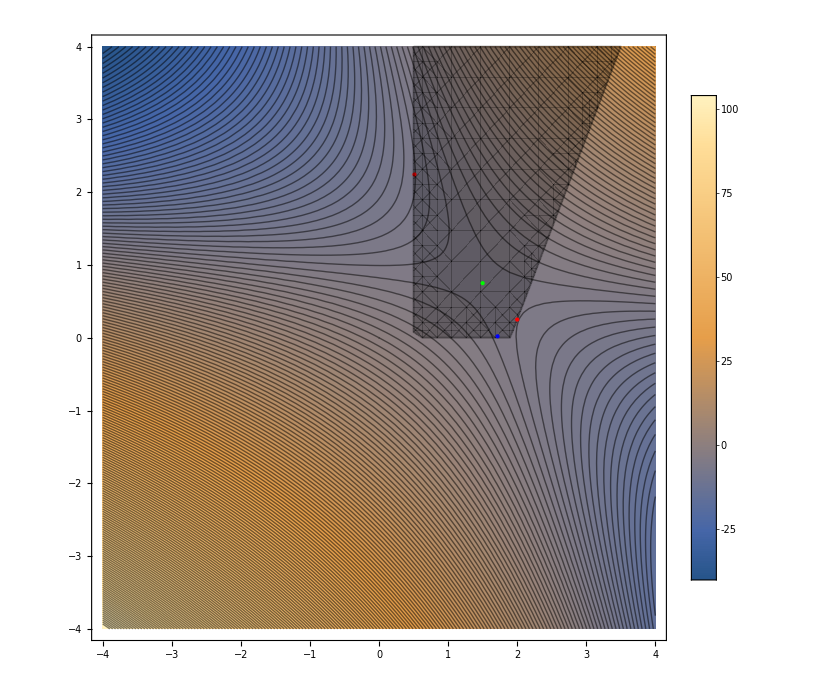

-6.5

```mathematica
pl1 = ContourPlot[f[x1,x2],{x1,-4,4},{x2,-4,4}, ImageSize->500,PlotLegends->Automatic,Contours->200];
pl2 = RegionPlot[{-5/2 x1+x2+19/4≥0&&x1-1/2≥0&&x2 1/2≥0},{x1,-4,4},{x2,-4,4},BoundaryStyle->Directive[Black,Opacity[0.25]],PlotStyle->Directive[Black,Opacity[0.25]]];
pmin1 = Graphics[{PointSize[Large],Red,Point[{1/2,9/4}]}];
pmin2 = Graphics[{PointSize[Large],Red,Point[{2,1/4}]}];
pindef = Graphics[{PointSize[Large],Green,Point[{3/2,3/4}]}];
ptest = Graphics[{PointSize[Large],Blue,Point[{1.7158,0.0197}]}];
Show[pl1,pl2,pmin1,pmin2,pindef,ptest,ImageSize->700,Method->{"TransparentPolygonMesh"->True}]
f[1./2,9/4]
```

```mathematica
H=({{1/2, 3}, {3, 2}});
x=({{x1}, {x2}});
Expand@(1/2)Transpose[x].H.x
```

{{1/2 (x2 (3 x1+2 x2)+x1 (x1/2+3 x2))}}

```mathematica
Expand[1/2 (x2 (3 x1+2 x2)+x1 (x1/2+3 x2))]
```

x1^2/4+3 x1 x2+x2^2